# Problem Session 1: Limits and functions

## Problem 1

```mathematica
x^2+2/.x->5
```

27

```mathematica
Limit[x^2+2,x->5]
```

27

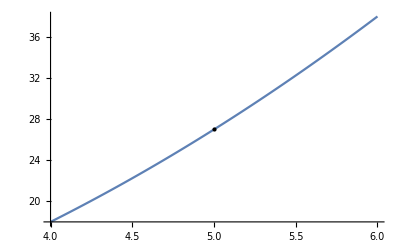

-Graphics-

```mathematica
Plot[x^2+2,{x,4,6},Epilog->{Black,PointSize[Large],Point[{5,27}]}]
Plot[x^2+2,{x,4,6},Epilog->{Black,PointSize[Large],Point[{5,27}]}]
```

```mathematica
v = {{1,1},{1,2}}
```

{{1,1},{1,2}}

```mathematica
Max[v]
```

2

```mathematica
Norm[v]
```

√(1/2 (7+3 √5))

```mathematica
Norm[v,2]
```

√(1/2 (7+3 √5))

```mathematica
Norm[v, Infinity]
```

3

## Problem 2

```mathematica
Limit[Sin[2x]-1,x->π/6,Direction->"FromBelow"]
```

-1+(√3)/2

```mathematica
Limit[Sin[2x]-1,x->π/6,Direction->"FromAbove"]
```

-1+(√3)/2

```mathematica
Limit[Sin[2x]-1,x->π/6]
```

-1+(√3)/2

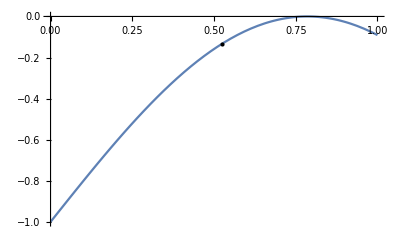

```mathematica
Plot[Sin[2x]-1,{x,0,1},Epilog->{Black,PointSize[Large],Point[{Pi/6,Sqrt[3]/2-1}]}]
```

## Problem 3

```mathematica
Limit[Log[2,x]-Exp[5x],x->8,Direction->"FromBelow"]//FullSimplify
```

3-ⅇ^40

```mathematica
Limit[Log[2,x]-Exp[5x],x->8,Direction->"FromAbove"] //FullSimplify
```

3-ⅇ^40

```mathematica
Limit[Log[2,x]-Exp[5x],x->8]//FullSimplify
```

3-ⅇ^40

```mathematica
N[%]
```

-2.35385×10^17

```mathematica
Plot[Log[2,x]-Exp[5x],{x,7.9,8.1},
Epilog-> {Black,PointSize[Large],Point[{8,3-Exp[40]}]}]
```

-Graphics-

## Problem 4

```mathematica
Limit[3/x,x->0,Direction->"FromBelow"]
```

-∞

```mathematica
Limit[3/x,x->0,Direction->"FromAbove"]
```

∞

```mathematica
Limit[3/x,x-> 0]
```

Indeterminate

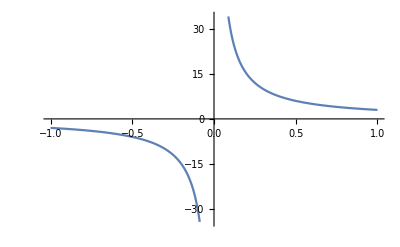

```mathematica
Plot[3/x,{x,-1,1}]
```

## Problem 5

```mathematica
x^2-7x+10/.x->2
```

0

can’t use Quotient law because at x = 2 the denominator is 0

So, let’s factor the equation.

```mathematica
Simplify[(3x-6)/(x^2-7x+10)]
```

3/(-5+x)

```mathematica
-5+x/. x->2
```

-3

```mathematica
3/(-5+x)/. x->2
```

-1

```mathematica
Limit[(3x-6)/(x^2-7x+10),x->2]
```

-1

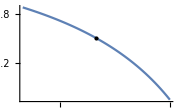

```mathematica
Plot[(3x-6)/(x^2-7x+10),{x,1,3},Sequence[Epilog->{Black,PointSize[Large],Point[{2,-1}]}, ImageSize->Small]]
```

## Problem 6

```mathematica
Limit[(6x-1)/(x^3-2x-1),x->3]
```

17/20

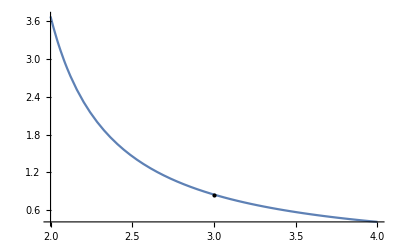

```mathematica
Plot[(6x-1)/(x^3-2x-1),{x,2,4},
Epilog->{Black,PointSize[Large],
Point[{3,17/20}]}]
```

## Problem 7

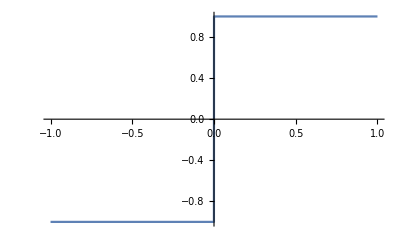

```mathematica
Plot[x/RealAbs[x],{x,-1,1}]
```

```mathematica
{Limit[x/RealAbs[x],x->0,Direction->"FromBelow"],
Limit[x/RealAbs[x],x->0,Direction->"FromAbove"]}
```

{-1,1}

```mathematica
Limit[x/RealAbs[x],x->0]
```

Indeterminate

## Problem 8

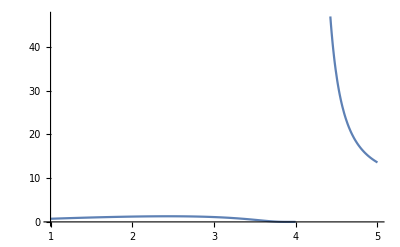

```mathematica
Plot[x Exp[1/(x-4)],{x,1,5}]
```

```mathematica
Grid[{{5,4.5,4.1,4.01,4.001},
Table[i Exp[1/(i-4)],
{i,{5,4.5,4.1,4.01,4.001}}]},Frame->All]
```

5 | 4.5 | 4.1 | 4.01 | 4.001
5 ⅇ | 33.2508 | 90308.5 | 1.07793×10^44 | 7.88225452455033×10^434

## Problem 9

```mathematica
f[x_]:=Piecewise[{{x^3-2x,x≠2}}, 6]
```

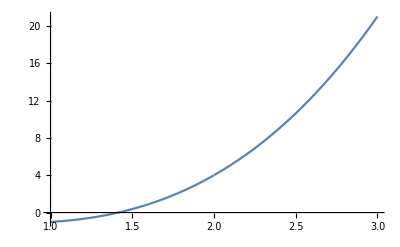

```mathematica
Plot[f[x],{x,1,3}]
```

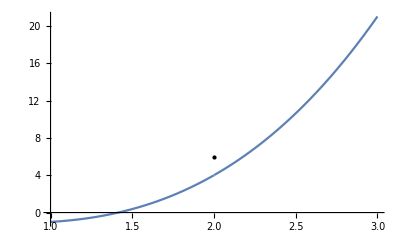

```mathematica
Plot[f[x],{x,1,3},Epilog->{Black,PointSize[Large],Point[{2,f[2]}]}]
```

```mathematica
{Limit[f[x],x->2,Direction->"FromBelow"],
Limit[f[x],x->2,Direction->"FromAbove"]}
```

{4,4}

```mathematica
Limit[f[x],x->2]
```

4

## Problem 10

```mathematica
f[x_]:=Piecewise[{{x-5,x<-3},{6/(x+4),x>=-3}}]
```

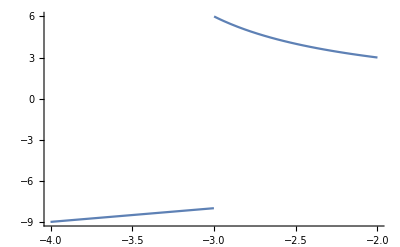

```mathematica
Plot[f[x],{x,-4,-2}]
```

```mathematica
f[x_]:=Piecewise[{{x-5,x<-3},{6/(x+4),x>=-3}}]
```

```mathematica
Plot[f[x],{x,-4,-2}]
```

-Graphics-

```mathematica
{Limit[f[x],x->-3, Direction->"FromBelow"],
Limit[f[x],x->-3,Direction->"FromAbove"]}
```

{-8,6}

```mathematica
Limit[f[x],x->-3]
```

Indeterminate

## Problem 11

```mathematica
FunctionDomain[Cos[x]+2x,x]
```

True

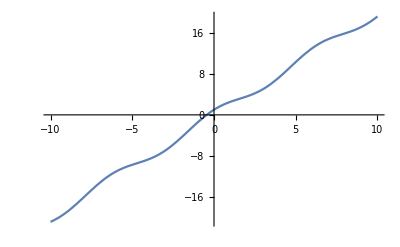

```mathematica
Plot[Cos[x]+2x,{x,-10,10}]
```

## Problem 12

```mathematica
x^2-4 /.x ->2
```

0

```mathematica
Factor[x^2-4]
```

(-2+x) (2+x)

```mathematica
Solve[x^2-4==0,x]
```

{{x→-2},{x→2}}

```mathematica
FunctionDomain[(x^2-2)/(x^2-4),x]
```

x<-2||-2<x<2||x>2

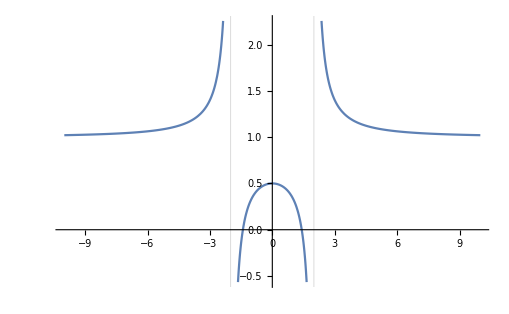

```mathematica
Plot[(x^2-2)/(x^2-4),{x,-10,10},GridLines->{{-2,2},None}]
```

## Problem 13

Compute the range of x^3. 
x^3 is an odd polynomial, so its range is all real numbers.

```mathematica
FunctionRange[x^3, x, y]
```

True

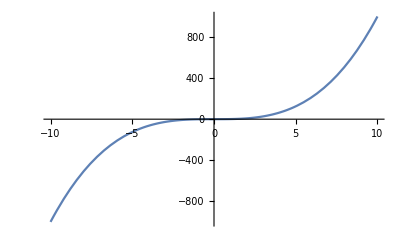

```mathematica
Plot[x^3, {x,-10,10}]
```

### Problem 14

Compute the range of Sec[x].
Secant is reciprocal of cosine, and cosine’s range is between 1 and -1.
This can be seen in the plot of cosine.

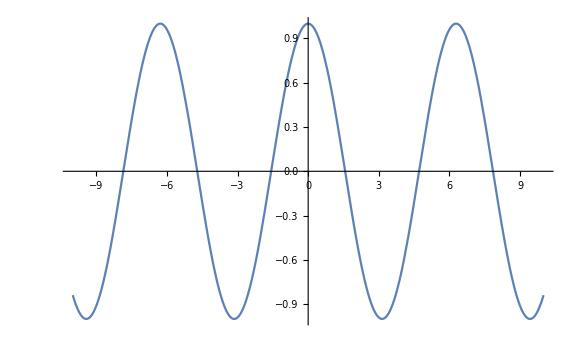

```mathematica
Plot[Cos[x],{x,-10,10},ImageSize->Large]
```

```mathematica
FunctionRange[Sec[x],x,y]
```

y≤-1||y≥1

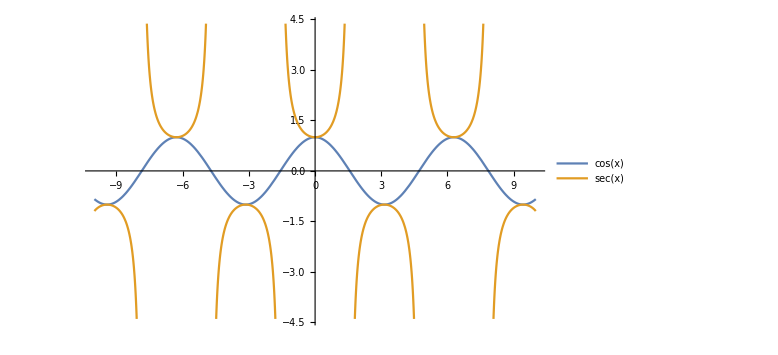

```mathematica
Plot[{Cos[x],Sec[x]},{x,-10,10},PlotLegends->"Expressions",
ImageSize->Large]
```